## Вычеты и их применение.

### Теоремы о вычетах и их применение к вычислению конурных интегралов.

№12.433 Используя теоремы о вычетах, вычислить следующий интеграл:

∫_(C^-) 1/(z^4+1)ⅆz,  C={z | |z-1|=1}

Для этого воспользуемся Первой теоремой о вычетах:

∫_(С^-) f(z)ⅆz=-2πⅈ∑_(k=1)^N res(f(z);z_k)

Найдем все полюса функции f(z)

```mathematica
f[z_]:=1/(z^4+1)
```

```mathematica
sol=Solve[z^4+1==0,z]
```

{{z→-(-1)^(1/4)},{z→(-1)^(1/4)},{z→-(-1)^(3/4)},{z→(-1)^(3/4)}}

В соответствии с условиями задачи, определим аналитически все полюса, находящиеся внутри контура С, или другими словами, растояние до которых от центра окружности (1,0) меньше или равно 1, и дадим этому графическую иллюстрацию. рис.1

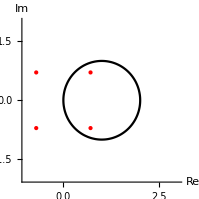

```mathematica
Show[ ContourPlot[(x-1)^2+y^2==1,{x,0,2},{y,-1,1},AxesLabel->{Re,Im},PlotRange->{{-1,3},{-2,2}} ,Frame->False,Axes->True],Graphics[{PointSize[Large],Red,Point[ReIm[z/.sol]]} ] ]
```

Найдем интеграл просуммировав вычеты во всех этих полюсах.

```mathematica
int=-2π ⅈ Sum [ If[ Abs[ -1+z/.sol[[i]]]≤ 1,Residue[f[z],{z,z/.sol[[i]] } ],0],{i,1,Length[z/.sol]} ]
```

```mathematica
-2 ⅈ (-1/4 (-1)^(1/4)+1/4 (-1)^(3/4)) π//ComplexExpand
```

(ⅈ π)/(√2)

Таким образом, получили ответ:

∫_(C^-) 1/(z^4+1)ⅆz=(ⅈ π)/(√2)